```mathematica
(*  AQC // Matthew Berntson //  4/12/16 *)
```

```mathematica
Clear["Global`*"]
```

```mathematica
sz={{1,0},{0,-1}};
sx={{0,1},{1,0}};
ID=IdentityMatrix[2];
```

### Example for the Facility Location problem, using an Ising Hamiltonian derived from a binary programming formulation. For the Ising Hamiltonian, the spin couplings: J_{ij} = 2*A*Sum_{j=1}^m S_ji S_jl for i!=j, and J_{ii} = A*Sum_{j=1}^m S_ji^2 for i==j . The magnetic field parameters: h_{i} = B*c_i + 2*A*Sum_{j=1}^m b_j S_ji.

```mathematica
(* The data for the matrices of cost (c), coupling (S), and constraint (b) are as follows *)
```

```mathematica
(* Number of binary variables *)
```

```mathematica
Num=5;
```

```mathematica
(* Number of constraints *)
```

```mathematica
m=1;
```

```mathematica
(* constants A and B are dictated by Num, s.t. A/B~>N *)
```

```mathematica
A=Num;
B=1;
```

```mathematica
(* c is the cost vector (want to maximize so use +1) *)
```

```mathematica
c = 1*{9,5,6,4,0};
```

```mathematica
(* S is the matrix of constraints (lhs) for the system of eqns *)
```

```mathematica
S ={{6,3,5,2,-1}};
```

```mathematica
(* b is the array of constraints (rhs) *)
```

```mathematica
b ={10};
```

```mathematica
(* Now calculate coupling and field parameters *)
```

```mathematica
(* Field Parameters *)
```

```mathematica
h={0,0,0,0,0};
```

```mathematica
For[i=1,i<Num+1,i++,h[[i]]=B*c[[i]]+2*A*Sum[b[[j]]*S[[j]][[i]],{j,m}]]
```

```mathematica
MatrixForm[h]
```

(609
305
506
204
-100)

```mathematica
(* Coupling Terms *)
```

```mathematica
J={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
```

```mathematica
(* Calculate all elements using the i≠l formula *)
```

```mathematica
For[l=1,l<Num+1,l++,For[i=l,i<Num+1,i++,J[[l]][[i]]=2*A*Sum[S[[j]][[i]]*S[[j]][[l]],{j,m}]]]
```

```mathematica
MatrixForm[J]
```

(360 | 180 | 300 | 120 | -60
0 | 90 | 150 | 60 | -30
0 | 0 | 250 | 100 | -50
0 | 0 | 0 | 40 | -20
0 | 0 | 0 | 0 | 10)

```mathematica
(* Replace diagonal elements with i==j formula *)
```

```mathematica
For[i=1,i<Num+1,i++,J[[i]][[i]]=A*Sum[S[[j]][[i]]*S[[j]][[i]],{j,m}]]
```

```mathematica
MatrixForm[J]
```

(180 | 180 | 300 | 120 | -60
0 | 45 | 150 | 60 | -30
0 | 0 | 125 | 100 | -50
0 | 0 | 0 | 20 | -20
0 | 0 | 0 | 0 | 5)

```mathematica
(* Hard code the spins *)
```

```mathematica
(* Note that the spins for the diagonal coupling terms are z_{i}^2 *)
```

```mathematica
z1=KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,ID]]]];
```

```mathematica
z2=KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[ID,ID]]]];
```

```mathematica
z3=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[ID,ID]]]];
```

```mathematica
z4=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sz,ID]]]];
```

```mathematica
z5=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,sz]]]];
```

```mathematica
z12=KroneckerProduct[sz,KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[ID,ID]]]];
```

```mathematica
z13=KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[ID,ID]]]];
```

```mathematica
z14=KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sz,ID]]]];
```

```mathematica
z15=KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,sz]]]];
```

```mathematica
z23=KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[sz,KroneckerProduct[ID,ID]]]];
```

```mathematica
z24=KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[sz,ID]]]];
```

```mathematica
z25=KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[ID,sz]]]];;
```

```mathematica
z34=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[sz,ID]]]];
```

```mathematica
z35=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[ID,sz]]]];;
```

```mathematica
z45=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sz,sz]]]];
```

```mathematica
(* Add field terms to problem hamiltonian *)
```

```mathematica
hp=-1*(h[[1]]z1+h[[2]]z2+h[[3]]z3+h[[4]]z4+h[[5]]z5);
```

```mathematica
(* Add coupling terms to problem hamiltonian *)
```

```mathematica
hp+=-1*(J[[1]][[1]] z1^2+J[[1]][[2]] z12+J[[1]][[3]] z13+J[[1]][[4]] z14+J[[1]][[5]]z15+J[[2]][[2]] z2^2+J[[2]][[3]]z23+J[[2]][[4]]z24+J[[2]][[5]]z25+J[[3]][[3]] z3^2+J[[3]][[4]]z34+J[[3]][[5]]z35+J[[4]][[4]] z4^2+J[[4]][[5]]z45+J[[5]][[5]] z5^2);
```

```mathematica
MatrixForm[hp]
```

(-2649 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -3169 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1721 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2161 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -637 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -957 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -109 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -349 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1319 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1719 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -631 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -951 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 93 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -107 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 381 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 261 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -351 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -631 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 97 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -103 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 461 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 381 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 509 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 509 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 259 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 99 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 467 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 387 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 471 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 511 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 279 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 399)

```mathematica
Eigenvalues[hp] (* of course, the problem Hamiltonian is diagonal: *)
```

{-3169,-2649,-2161,-1721,-1719,-1319,-957,-951,-637,-631,-631,511,509,509,471,467,461,399,387,381,381,-351,-349,279,261,259,-109,-107,-103,99,97,93}

```mathematica
x12=KroneckerProduct[sx,KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[ID,ID]]]];;
```

```mathematica
x13=KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[ID,ID]]]];;
```

```mathematica
x14=KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sx,ID]]]];;
```

```mathematica
x15=KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,sx]]]];;
```

```mathematica
x23=KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[sx,KroneckerProduct[ID,ID]]]];
```

```mathematica
x24=KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[sx,ID]]]];
```

```mathematica
x25=KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[ID,sx]]]];
```

```mathematica
x34=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[sx,ID]]]];
```

```mathematica
x35=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[ID,sx]]]];
```

```mathematica
x45=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sx,sx]]]];
```

```mathematica
hinit=-1*(x12+x13+x14+x15+x23+x24+x25+x34+x35+x45) ;(* placeholder initial Hamiltonian, something simpler would be more practical *)
```

```mathematica
MatrixForm[hinit]
```

(0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
-1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
-1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0
-1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0
-1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0
0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1
-1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1
0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1
0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0
0 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0
-1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0
-1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0
0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1
-1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1
0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1
0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0)

```mathematica
Eigenvalues[hinit]
```

{-10,-10,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
htot[s_]:=s hp+(1-s) hinit
```

```mathematica
MatrixForm[htot[s]]
```

(-2649 s | 0 | 0 | -1+s | 0 | -1+s | -1+s | 0 | 0 | -1+s | -1+s | 0 | -1+s | 0 | 0 | 0 | 0 | -1+s | -1+s | 0 | -1+s | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -3169 s | -1+s | 0 | -1+s | 0 | 0 | -1+s | -1+s | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | 0 | 0
0 | -1+s | -1721 s | 0 | -1+s | 0 | 0 | -1+s | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | 0
-1+s | 0 | 0 | -2161 s | 0 | -1+s | -1+s | 0 | 0 | -1+s | -1+s | 0 | 0 | 0 | 0 | -1+s | 0 | -1+s | -1+s | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | 0
0 | -1+s | -1+s | 0 | -637 s | 0 | 0 | -1+s | -1+s | 0 | 0 | 0 | 0 | -1+s | -1+s | 0 | -1+s | 0 | 0 | 0 | 0 | -1+s | -1+s | 0 | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | 0
-1+s | 0 | 0 | -1+s | 0 | -957 s | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | 0 | -1+s | 0 | 0
-1+s | 0 | 0 | -1+s | 0 | -1+s | -109 s | 0 | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | 0 | 0 | -1+s | 0
0 | -1+s | -1+s | 0 | -1+s | 0 | 0 | -349 s | 0 | 0 | 0 | -1+s | 0 | -1+s | -1+s | 0 | 0 | 0 | 0 | -1+s | 0 | -1+s | -1+s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1+s
0 | -1+s | -1+s | 0 | -1+s | 0 | 0 | 0 | -1319 s | 0 | 0 | -1+s | 0 | -1+s | -1+s | 0 | -1+s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1+s | -1+s | 0 | -1+s | 0 | 0 | 0
-1+s | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | 0 | -1719 s | -1+s | 0 | -1+s | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | -1+s | 0 | 0
-1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | -631 s | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0
0 | -1+s | -1+s | 0 | 0 | 0 | 0 | -1+s | -1+s | 0 | 0 | -951 s | 0 | -1+s | -1+s | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | 0 | -1+s | -1+s | 0 | 0 | 0 | 0 | -1+s
-1+s | 0 | 0 | 0 | 0 | -1+s | -1+s | 0 | 0 | -1+s | -1+s | 0 | 93 s | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | -1+s | -1+s | 0
0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | -1+s | 0 | 0 | -1+s | 0 | -107 s | -1+s | 0 | 0 | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s
0 | 0 | -1+s | 0 | -1+s | 0 | 0 | -1+s | -1+s | 0 | 0 | -1+s | 0 | -1+s | 381 s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | -1+s
0 | 0 | 0 | -1+s | 0 | -1+s | -1+s | 0 | 0 | -1+s | -1+s | 0 | -1+s | 0 | 0 | 261 s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | -1+s | 0 | -1+s | -1+s | 0
0 | -1+s | -1+s | 0 | -1+s | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -351 s | 0 | 0 | -1+s | 0 | -1+s | -1+s | 0 | 0 | -1+s | -1+s | 0 | -1+s | 0 | 0 | 0
-1+s | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -631 s | -1+s | 0 | -1+s | 0 | 0 | -1+s | -1+s | 0 | 0 | -1+s | 0 | -1+s | 0 | 0
-1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | 0 | 0 | -1+s | 97 s | 0 | -1+s | 0 | 0 | -1+s | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0
0 | -1+s | -1+s | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | -103 s | 0 | -1+s | -1+s | 0 | 0 | -1+s | -1+s | 0 | 0 | 0 | 0 | -1+s
-1+s | 0 | 0 | 0 | 0 | -1+s | -1+s | 0 | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | -1+s | -1+s | 0 | 461 s | 0 | 0 | -1+s | -1+s | 0 | 0 | 0 | 0 | -1+s | -1+s | 0
0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | 381 s | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s
0 | 0 | -1+s | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | -1+s | 0 | -1+s | 509 s | 0 | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | -1+s
0 | 0 | 0 | -1+s | 0 | -1+s | -1+s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1+s | 0 | -1+s | -1+s | 0 | -1+s | 0 | 0 | 509 s | 0 | 0 | 0 | -1+s | 0 | -1+s | -1+s | 0
-1+s | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1+s | -1+s | 0 | -1+s | 0 | 0 | 0 | 0 | -1+s | -1+s | 0 | -1+s | 0 | 0 | 0 | 259 s | 0 | 0 | -1+s | 0 | -1+s | -1+s | 0
0 | -1+s | 0 | 0 | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | 0 | 99 s | -1+s | 0 | -1+s | 0 | 0 | -1+s
0 | 0 | -1+s | 0 | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 467 s | 0 | -1+s | 0 | 0 | -1+s
0 | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | 0 | -1+s | -1+s | 0 | 0 | 0 | 0 | -1+s | 0 | -1+s | -1+s | 0 | 0 | 0 | 0 | -1+s | -1+s | 0 | 0 | 387 s | 0 | -1+s | -1+s | 0
0 | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | 0 | -1+s | -1+s | 0 | -1+s | 0 | 0 | 0 | 0 | -1+s | -1+s | 0 | 0 | -1+s | -1+s | 0 | 471 s | 0 | 0 | -1+s
0 | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | -1+s | 0 | 0 | -1+s | 0 | 511 s | -1+s | 0
0 | 0 | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | -1+s | 0 | 0 | -1+s | 0 | -1+s | 0 | 0 | -1+s | -1+s | 0 | 0 | -1+s | 0 | -1+s | 279 s | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1+s | 0 | 0 | 0 | -1+s | 0 | -1+s | -1+s | 0 | 0 | 0 | 0 | -1+s | 0 | -1+s | -1+s | 0 | 0 | -1+s | -1+s | 0 | -1+s | 0 | 0 | 399 s)

```mathematica
evals=Eigenvalues[htot[s]];
```

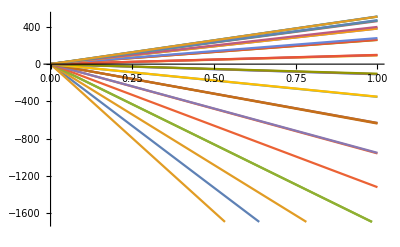

```mathematica
Plot[evals,{s,0,1}]
```

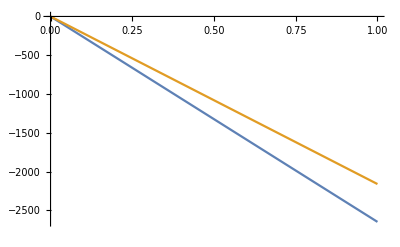

```mathematica
Plot[{evals[[1]],evals[[2]]},{s,0,1}]
```

```mathematica
nppgap[s_]:=evals[[1]]-evals[[2]]
```

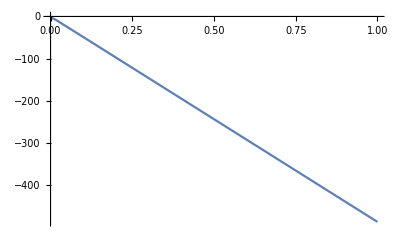

```mathematica
Plot[nppgap[s],{s,0,1}]
```

```mathematica
(* Ground state of the final hamiltonian (s=1) *)
```

```mathematica
MatrixForm[Eigenvectors[htot[1]][[1]]]
```

(0
1
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)

```mathematica
up={{1},{0}};
down={{0},{1}};
MatrixForm[up]
MatrixForm[down]
```

(1
0)

(0
1)

```mathematica
MatrixForm[KroneckerProduct[up,KroneckerProduct[up,KroneckerProduct[up,KroneckerProduct[up,down]]]]]
```

(0
1
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)

```mathematica
(* This is the same state as the ground state of the final hamiltonian *)
```

```mathematica
(* Therefore the solution using this method is x1=x2=x3=x4=1, x5=0.  This is unfortunate, as these values clearly do not meet the equality constraint.  Perhaps there is an error in building the problem Hamiltonian *)
```